```mathematica
sphere[x_]:=Module[
{},Sum[(x[[i]])^2,{i,Length@x}]]
```

```mathematica
DE[f_,dim_]:=Module[{},
G1=RandomReal[{-500,500},{20,dim}];
CR=Table[0.9,20];
F=Table[0.5,20];
solution={};
G={};

For[k=1,k<=100,k++,
AppendTo[solution,Min@Table[f[G1[[i]]],{i,20}]];
AppendTo[G,G1];
(*Mutation*)

GRest=Table[Complement[G1,{G1[[i]]}],{i,20}];
Table[Length@GRest[[i]],{i,20}];
R2=Table[RandomChoice[GRest[[i]]],{i,20}];
R1=G1;
GRest2=Table[Complement[G1,{R1[[i]]},{R2[[i]]}],{i,20}];
R3=Table[RandomChoice[GRest2[[i]]],{i,20}];
GRest3=Table[Complement[G1,{R1[[i]]},{R2[[i]]},{R3[[i]]}],{i,20}];
R4=Table[RandomChoice[GRest3[[i]]],{i,20}];
(*F and CR manipulation*)
FOrg=F;
CROrg=CR;
For[i=1,i<=20,i++,If[RandomReal[]<=0.1,F[[i]]=RandomReal[{0.1,0.9}]]];
For[i=1,i<=20,i++,If[RandomReal[]<=0.1,CR[[i]]=RandomReal[{0,1}]]];

MutantVector=Table[R2[[i]]+F[[i]]*(R3[[i]]-R4[[i]]),{i,20}];
(*Crossover*)
child=Table[Table[0,dim],20];
For[i=1,i<=20,i++,

jrand =RandomInteger[{1,dim}];
For[j=1,j<=dim,j++,If[RandomReal[{0,1}]<=CR[[i]]||j==jrand,child[[i]][[j]]=MutantVector[[i]][[j]],child[[i]][[j]]=R1[[i]][[j]]]]];
For[i=1,i<=20,i++,If[f[child[[i]]]<f[R1[[i]]],G1[[i]]=child[[i]],F[[i]]=FOrg[[i]];CR[[i]]=CROrg[[i]]]];


];
Return@solution
]
```

```mathematica
DE[sphere,10]
```

{512331.,375155.,375155.,375155.,375155.,358738.,358738.,158073.,158073.,93318.7,93318.7,93318.7,93318.7,93318.7,93318.7,93318.7,93318.7,93318.7,56514.5,56514.5,37372.9,37372.9,37372.9,36544.9,35414.4,25511.9,25511.9,25511.9,25511.9,23562.,23562.,14440.2,14440.2,14440.2,14440.2,10269.8,7211.48,7211.48,7211.48,7211.48,7211.48,7168.43,4738.49,4738.49,4738.49,4738.49,4565.71,4565.71,3935.11,3935.11,3935.11,3723.54,3547.13,3355.11,3355.11,1175.18,1175.18,585.009,585.009,585.009,585.009,514.288,514.288,451.098,451.098,434.174,434.174,434.174,434.174,147.616,147.616,147.616,147.616,147.616,147.616,147.616,147.616,147.616,147.616,147.616,69.9966,69.9966,69.9966,69.9966,69.9966,47.0259,47.0259,47.0259,47.0259,47.0259,47.0259,47.0259,47.0259,23.8926,23.8926,23.8926,23.8926,23.8926,23.8926,23.8926}

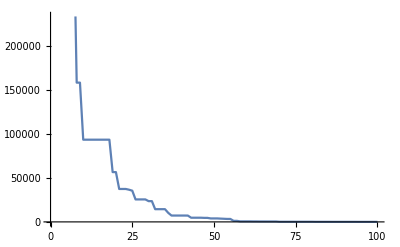

```mathematica
ListLinePlot@solution
```

```mathematica
(*SUM OF DIFFERENT POWERS FUNCTION*)
```

```mathematica
SDP[x_]:=Module[{l=Length@x},Sum[Abs[x[[i]]]^(i+1),{i,l}]]
```

```mathematica
(*SUM SQUARES FUNCTION*)
```

```mathematica
SS[x_]:=Module[{l=Length@x},Sum[i*(x[[i]]^2),{i,l}]]
```

```mathematica
(*TRID FUNCTION*)
```

```mathematica
Trid[x_]:=Module[{l=Length@x},Sum[(x[[i]]-1)^2,{i,l}]-Sum[x[[i]]*x[[i-1]],{i,2,l}]]
```

```mathematica
(*ROTATED HYPER-ELLIPSOID FUNCTION*)
```

```mathematica
RHE[x_]:=Module[{l=Length@x},Sum[Sum[x[[j]]^2,{j,i}],{i,l}]]
```

```mathematica
DE[SDP,10]
ListLinePlot@solution
```

{5.45924×10^22,5.45924×10^22,1.44378×10^21,1.44378×10^21,2.35647×10^20,1.1214×10^20,1.1214×10^20,8.53666×10^19,1.28059×10^19,5.13581×10^18,5.13171×10^18,3.00519×10^18,2.43146×10^18,1.71259×10^18,4.96034×10^17,3.98266×10^17,3.53106×10^17,1.35383×10^17,1.26637×10^17,7.44473×10^16,1.23205×10^16,1.23205×10^16,4.57806×10^15,4.55723×10^15,3.81282×10^15,2.46076×10^15,2.05726×10^15,1.87503×10^15,9.48187×10^14,9.48187×10^14,9.48187×10^14,3.40055×10^14,3.40055×10^14,1.50076×10^14,1.50076×10^14,1.50076×10^14,1.50076×10^14,1.50076×10^14,1.35535×10^14,1.35535×10^14,1.30107×10^14,1.16061×10^14,1.01818×10^14,5.95357×10^13,5.95357×10^13,5.1933×10^13,5.1933×10^13,5.1933×10^13,4.398×10^13,3.18704×10^13,2.88418×10^13,2.78778×10^13,2.78778×10^13,2.47949×10^13,2.47949×10^13,2.32915×10^13,2.32915×10^13,2.10671×10^13,1.84054×10^13,1.84054×10^13,1.84054×10^13,1.84054×10^13,1.84054×10^13,1.84054×10^13,1.71166×10^13,1.67885×10^13,1.61559×10^13,1.29692×10^13,1.29692×10^13,1.24779×10^13,1.21827×10^13,1.21827×10^13,1.12243×10^13,1.0739×10^13,8.55148×10^12,8.55148×10^12,8.55148×10^12,7.05574×10^12,7.05574×10^12,6.37072×10^12,5.99154×10^12,3.45615×10^12,3.45615×10^12,3.45615×10^12,3.45615×10^12,3.45615×10^12,2.86472×10^12,2.84846×10^12,2.57156×10^12,2.17081×10^12,1.89241×10^12,1.68806×10^12,1.68806×10^12,1.03663×10^12,1.03663×10^12,1.03663×10^12,1.03663×10^12,8.00928×10^11,3.89053×10^11,2.07371×10^11}

-Graphics-

{2.56383×10^6,2.56383×10^6,2.56383×10^6,2.30664×10^6,846503.,846503.,846503.,846503.,846503.,846503.,846503.,699351.,699351.,699351.,645448.,523952.,523952.,523952.,523952.,523952.,386296.,386296.,381746.,365933.,304569.,304569.,237988.,237988.,207494.,55750.4,55750.4,53697.6,53697.6,53697.6,53697.6,53697.6,53697.6,40899.7,40899.7,40899.7,37021.1,37021.1,37021.1,37021.1,27975.4,27975.4,14246.7,14246.7,14246.7,10002.4,10002.4,10002.4,8958.92,8958.92,6528.34,6528.34,3221.32,3221.32,3113.04,3113.04,2900.91,2270.53,2270.53,2270.53,1428.21,1390.16,999.607,999.607,792.138,792.138,746.322,746.322,746.322,680.389,635.558,419.378,396.092,396.092,302.736,292.078,292.078,292.078,194.553,194.553,133.296,133.296,121.594,97.006,97.006,93.6516,93.6516,84.8495,66.1573,66.1573,63.6859,55.0289,55.0289,50.6917,17.5377,17.5377}

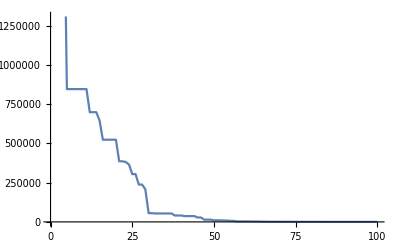

```mathematica
DE[SS,10]
ListLinePlot@solution
```

{377901.,218908.,218908.,218908.,218908.,218908.,133132.,133132.,133132.,133132.,133132.,133132.,133132.,80798.9,80798.9,80798.9,80798.9,80798.9,80798.9,80798.9,80798.9,80798.9,64971.7,49779.2,49779.2,49779.2,49779.2,42782.2,42782.2,30015.7,30015.7,30015.7,30015.7,30015.7,24217.3,16962.4,16962.4,16962.4,16962.4,16962.4,16962.4,16962.4,16962.4,14848.9,14848.9,14848.9,14021.1,14021.1,14021.1,9783.63,9783.63,9783.63,9783.63,9783.63,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2333.11,2308.75,1867.38,1830.48,1545.87,1545.87,1453.85,1453.85,1453.85,1453.85,1453.85,1453.85,517.44,517.44,418.477,418.477,282.117,282.117,282.117,282.117,282.117,282.117,282.117,282.117,282.117,253.886,253.886,253.886,210.847,210.847,210.847,210.847}

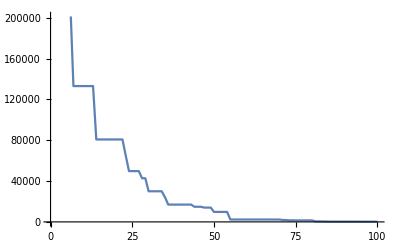

```mathematica
DE[Trid,10]
ListLinePlot@solution
```

{2.04044×10^6,2.04044×10^6,1.97552×10^6,1.76435×10^6,1.23271×10^6,1.22234×10^6,994103.,994103.,832750.,526629.,526629.,526629.,375554.,375554.,288521.,288521.,288521.,288521.,197617.,181387.,181387.,158676.,143714.,143714.,143714.,102760.,102760.,102760.,78844.,78844.,78844.,61096.4,61096.4,61096.4,36574.9,29922.7,29922.7,29922.7,29922.7,29922.7,29922.7,29922.7,17093.6,17093.6,17093.6,17093.6,12457.9,11227.8,8962.39,8962.39,8962.39,8962.39,8962.39,6685.6,3486.61,3486.61,2846.47,2846.47,2333.33,2333.33,2333.33,1401.84,1401.84,1292.38,1292.38,1157.89,1157.89,858.796,858.796,421.732,421.732,421.732,421.732,421.732,421.732,354.553,354.553,354.553,346.067,248.193,221.114,221.114,221.114,173.545,173.545,168.182,122.49,96.3452,92.6014,92.6014,92.6014,62.2711,62.2711,49.0906,47.5167,47.5167,37.7932,37.7932,26.1751,26.1751}

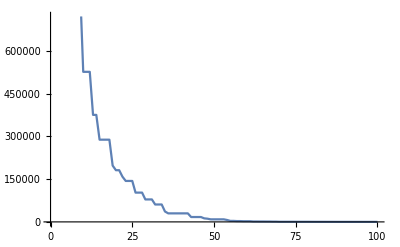

```mathematica
DE[RHE,10]
ListLinePlot@solution
```